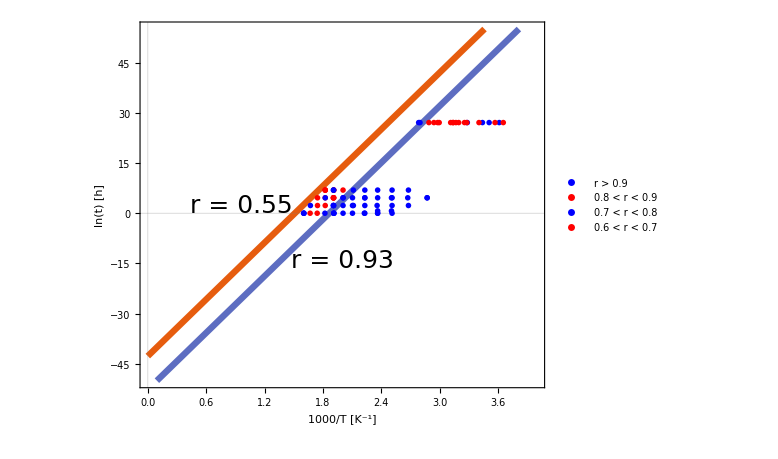
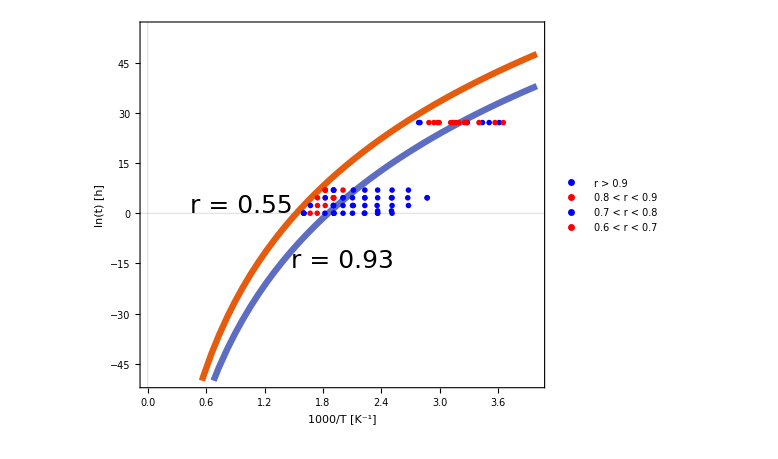
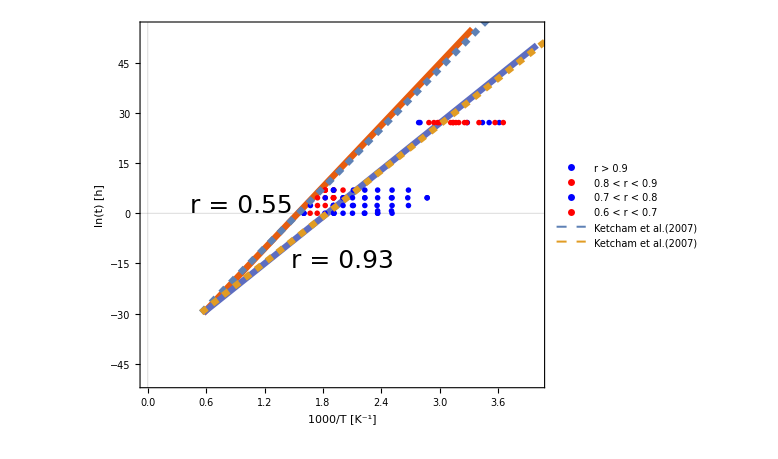
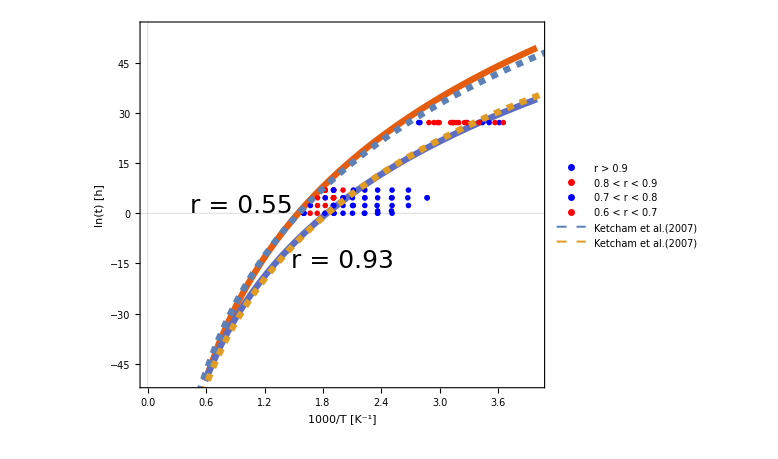
-Graphics- (a) PA-Graphics-   (b) PC-Graphics-   (c) FA-Graphics-   (d) FC

```mathematica
fig1=Print[Labeled[Show[pltPseudoArrhenius[[1]],DurangoPoints]," (a) PA",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[Show[pltPseudoArrhenius[[2]],DurangoPoints],"   (b) PC",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[ Show[pltPseudoArrhenius[[3]],DurangoPoints,pltPseudoArrheniusKet[[1]]],"   (c) FA",LabelStyle->Directive[Bold,  FontSize->30,FontFamily->"Computer Modern"]],
Labeled[ Show[pltPseudoArrhenius[[4]],DurangoPoints,pltPseudoArrheniusKet[[2]]],"   (d) FC",LabelStyle->Directive[Bold,  FontSize->30,FontFamily->"Computer Modern"]]
](**Fig.1**)
```

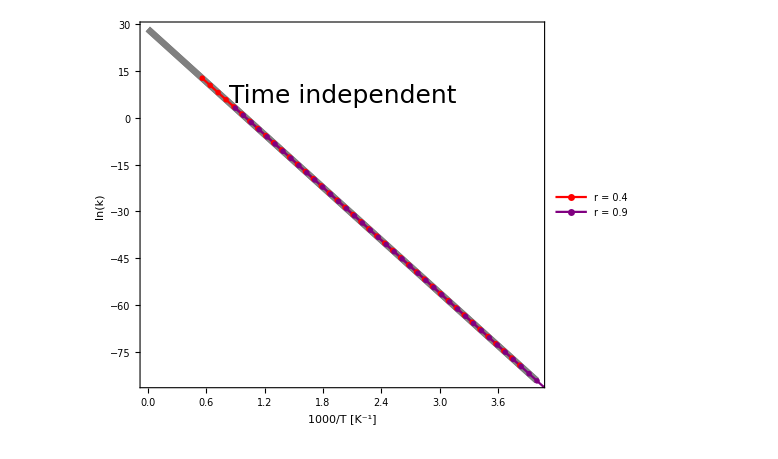
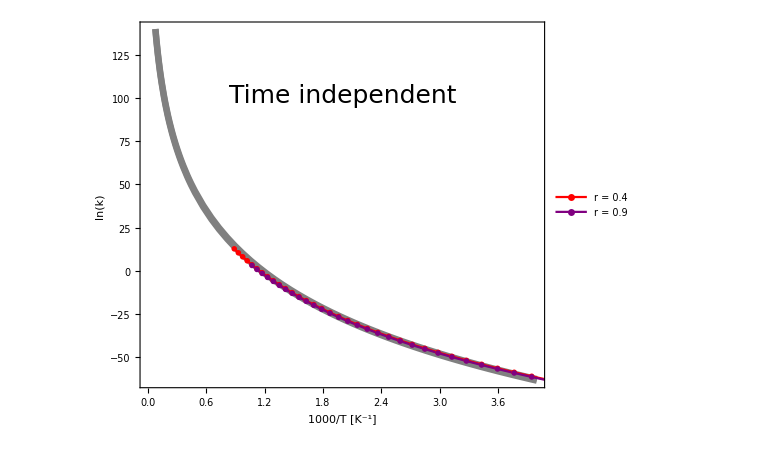
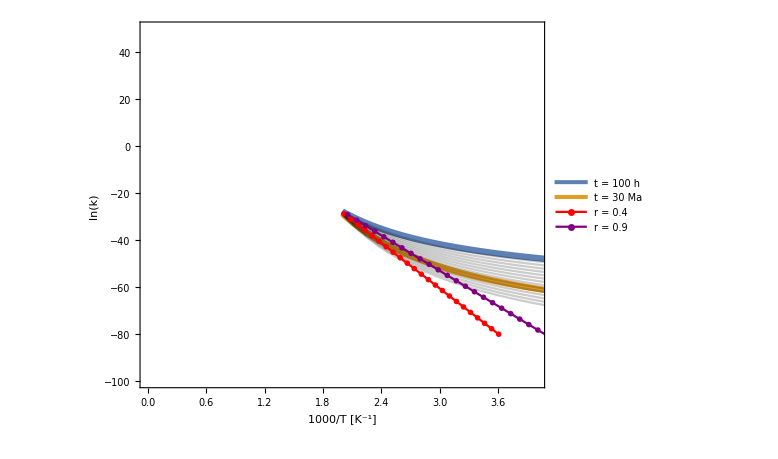
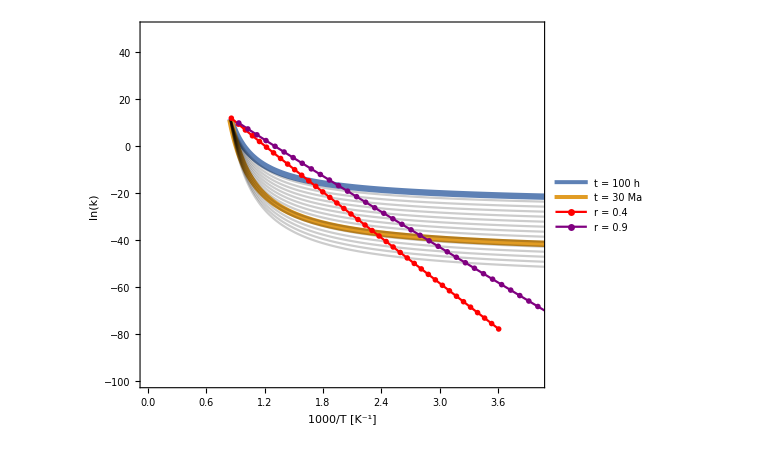
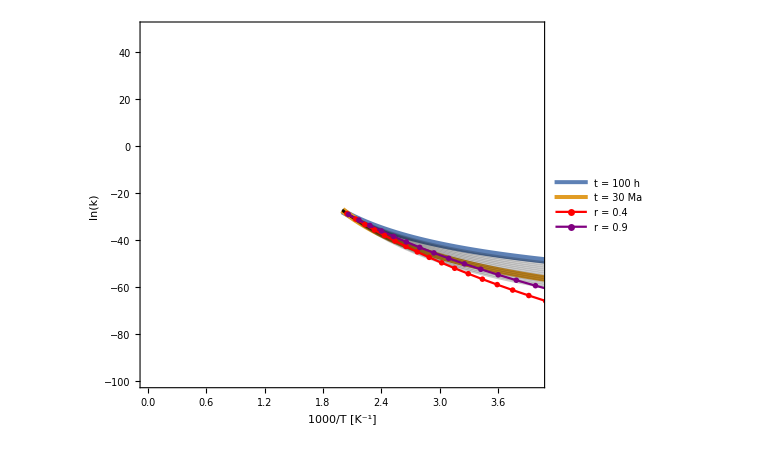
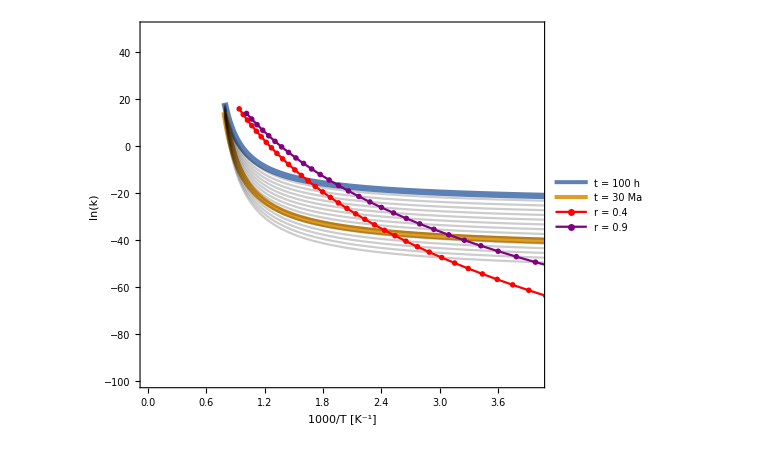
-Graphics- (a) PA-Graphics-   (b) PC-Graphics-   (c) FA(-4.36) -Graphics-   (d) FA(0) -Graphics-   (e) FC(-4.36)-Graphics-   (f) FC(0)

```mathematica
fig3=Print[Labeled[pltArrhenius[-4.36,0][[1]]," (a) PA",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[pltArrhenius[-4.36,0][[2]],"   (b) PC",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[pltArrhenius[-4.36,2][[3]],"   (c) FA(-4.36) ",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[pltArrhenius[0,0.85][[3]],"   (d) FA(0) ",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[ pltArrhenius[-4.36,2][[4]],"   (e) FC(-4.36)",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[ pltArrhenius[0,0.79][[4]],"   (f) FC(0)",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]]
];(**Fig.3**)
```

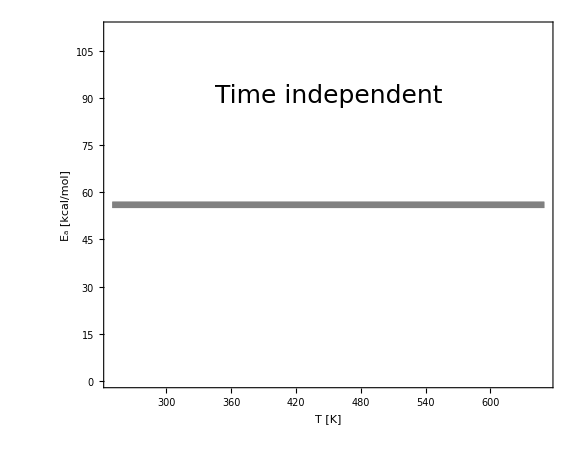
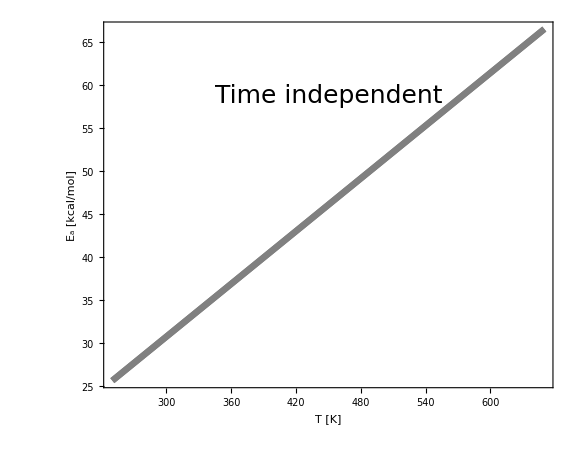
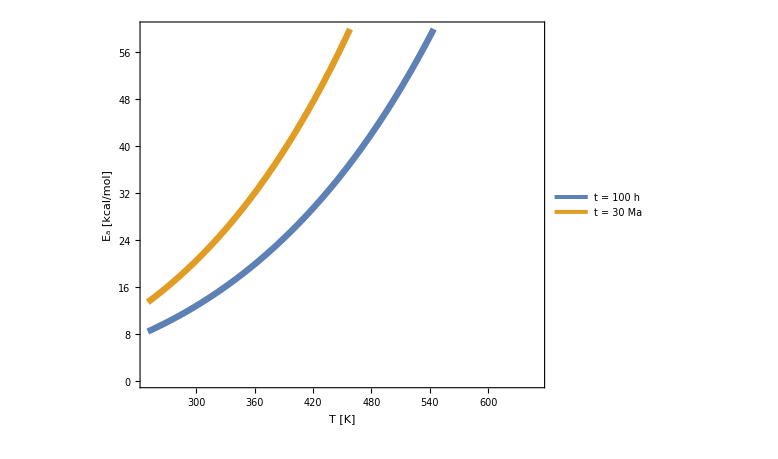
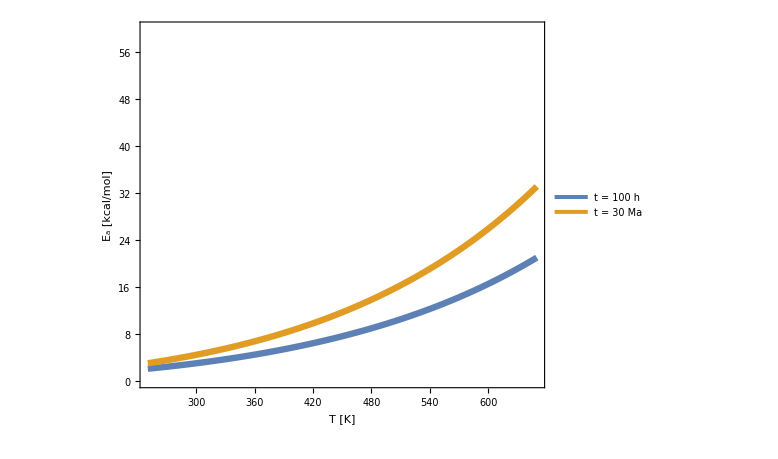
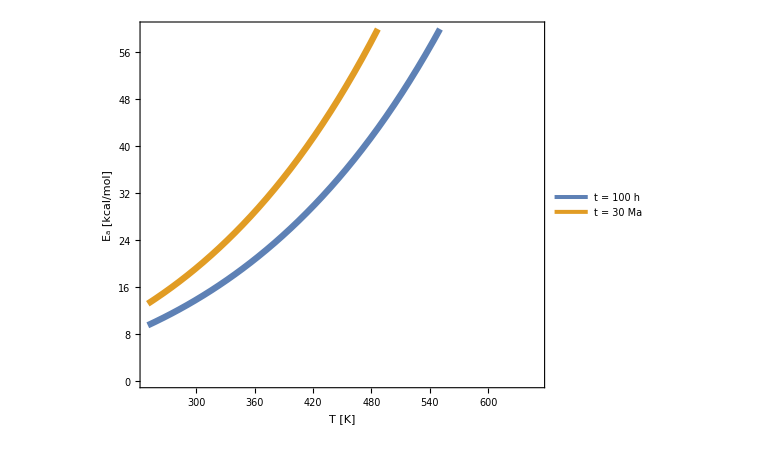
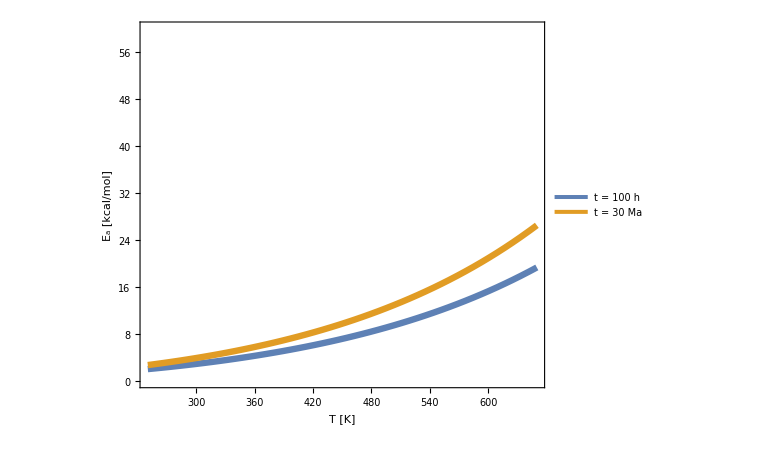
-Graphics- (a) PA-Graphics-   (b) PC-Graphics-   (c) FA(-4.36)-Graphics-   (d) FA(0)-Graphics-   (e) FC(-4.36)-Graphics-   (f) FC(0)

```mathematica
fig4=Print[Labeled[pltEa[-4.36][[1]]," (a) PA",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[pltEa[-4.36][[2]],"   (b) PC",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[pltEa[-4.36][[3]],"   (c) FA(-4.36)",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[pltEa[0][[3]],"   (d) FA(0)",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[ pltEa[-4.36][[4]],"   (e) FC(-4.36)",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[pltEa[0][[4]],"   (f) FC(0)",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]]
];(**Fig.4**)
```

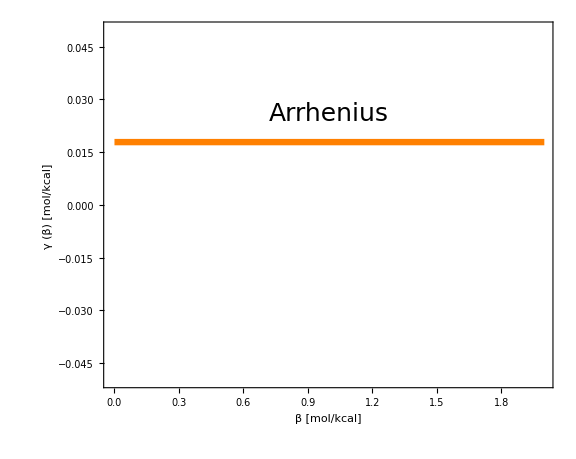
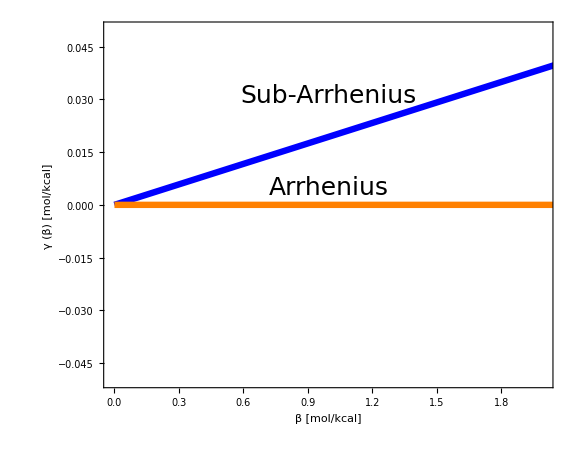
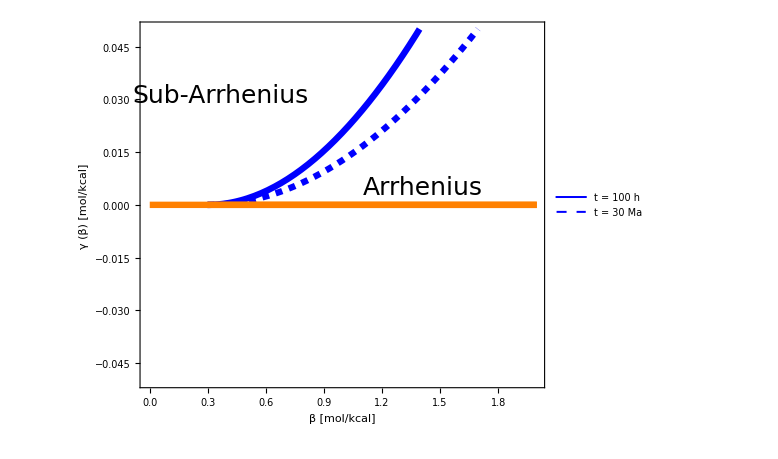
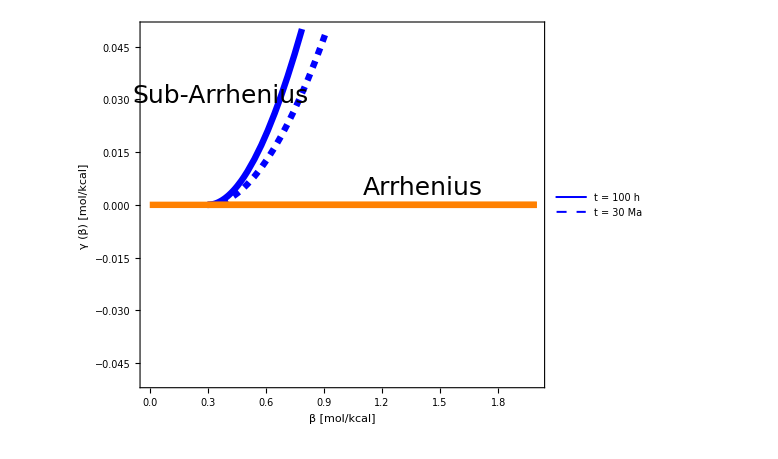
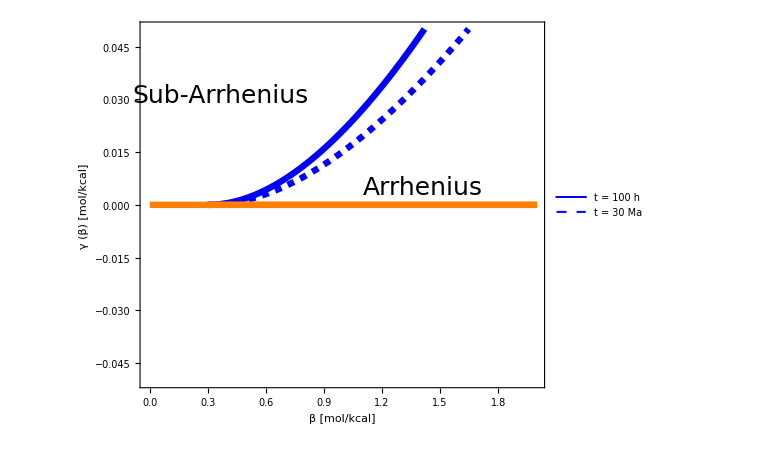
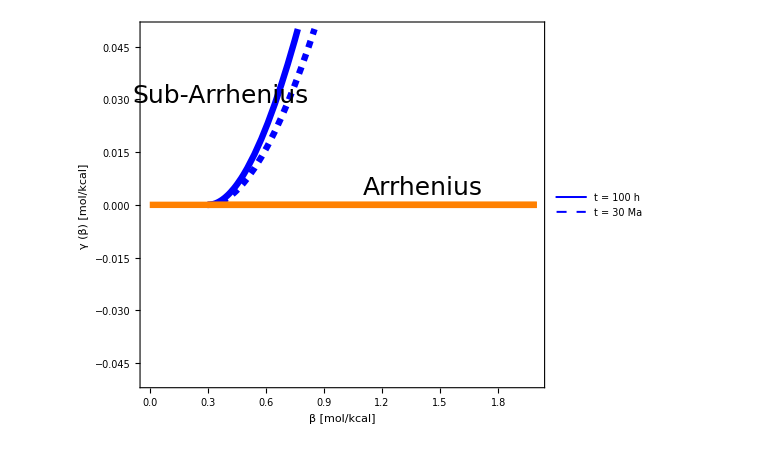
-Graphics- (a) PA-Graphics-   (b) PC-Graphics-   (c) FA(-4.36)-Graphics-   (d) FA(0)-Graphics-   (d) FC(-4.36)-Graphics-   (f) FC(0)

```mathematica
fig5=Print[Labeled[pltγ[-4.36][[1]]," (a) PA",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[pltγ[-4.36][[2]],"   (b) PC",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[pltγ[-4.36][[3]],"   (c) FA(-4.36)",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[pltγ[0][[3]],"   (d) FA(0)",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[ pltγ[-4.36][[4]],"   (d) FC(-4.36)",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]],
Labeled[ pltγ[0][[4]],"   (f) FC(0)",LabelStyle->Directive[Bold, FontSize->30,FontFamily->"Computer Modern"]]

];(**Fig.5**)
```

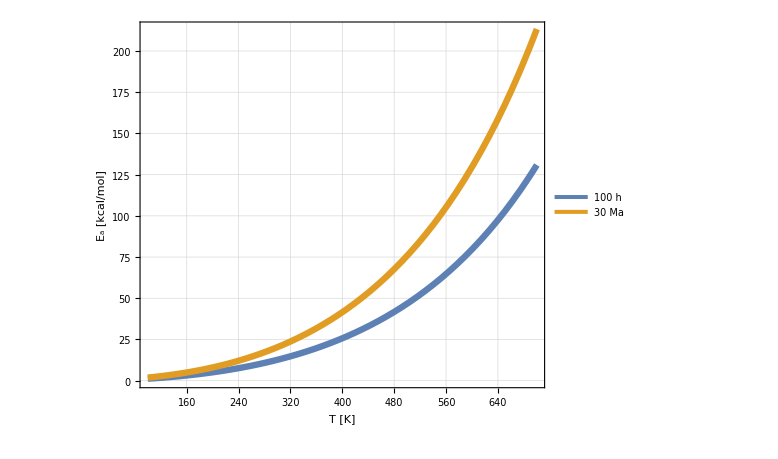

```mathematica
lgndEa=Plot[{Ea[tlab,T,-4.31][[3]],Ea[tgeo,T,-4.31][[3]]},{T,100,700},ops3,PlotLegends->{"100 h","30 Ma"}]
```

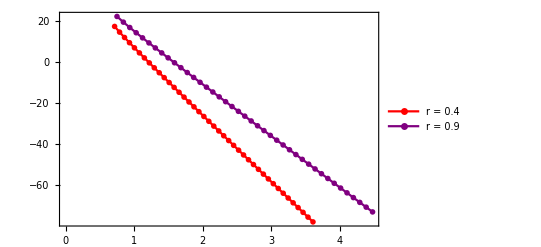

```mathematica
lgndarhh=ListPlot[{Select[Isoptscalc[0][[3,1]],(0<#[[1]]&)[[;;,1;;2]]],Select[Isoptscalc[3][[3,2]],(0<#[[1]]&)[[;;,1;;2]]]},ops22,PlotLegends->Placed[{"r = 0.4","r = 0.9"},Below],Frame->True]
```

```mathematica
fig5=Print[Labeled[pltArrhenius[0][[4]]," (a) n = 0",LabelStyle->Directive[Bold, FontSize->40]],
Labeled[pltArrhenius[-4][[4]],"   (b) n = -4",LabelStyle->Directive[Bold, FontSize->40]]
](**Fig.5**)
```

Part::partw: Part 4 of pltArrhenius[0] does not exist.

Part::partw: Part 4 of pltArrhenius[-4] does not exist.

pltArrhenius[0]⟦4⟧ (a) n = 0pltArrhenius[-4]⟦4⟧   (b) n = -4

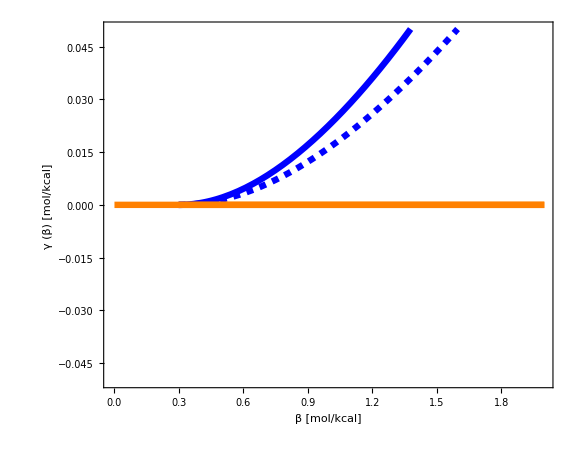

```mathematica
Show[Plot[{γ[tlab,β,-4][[4]],γ[tgeo,β,-4][[4]],0},{β,0.29845,2},PlotRange->{{-0.01,2},{-0.05,0.05}},ops4,PlotStyle->{{Blue,Thickness[0.0080]},{Blue,Dashed,Thickness[0.0080]},{Orange,Thickness[0.0080]}}],Plot[0,{β,0,2},PlotStyle->{Orange,Thickness[0.0080]}]]
```